```mathematica
(*FFCF breakdown into auto- and cross- correlations. Ask Casey for more information.*)
(*Takes output from slv_calc-tcf-mod*)
SetDirectory["/Users/Sherina/Desktop/2BBM-4.B-10ns-100.0ns-FFCF-1ps"];

(*Input data*)
(*auto-correlations*)
TotenvTotenvRaw = Import["tcf.TOTENV-TOTENV.unorm.dat","Table"];
CouCouRaw = Import["tcf.COU-COU.unorm.dat","Table"];
PolPolRaw=Import["tcf.POL-POL.unorm.dat","Table"];
ExrExrRaw=Import["tcf.EXR-EXR.unorm.dat","Table"];
DisDisRaw=Import["tcf.DIS-DIS.unorm.dat","Table"];
(*cross-correlations*)
CouPolRaw=Import["tcf.COU-POL.unorm.dat","Table"];
CouExrRaw=Import["tcf.COU-EXR.unorm.dat","Table"];
CouDisRaw=Import["tcf.COU-DIS.unorm.dat","Table"];
ExrPolRaw=Import["tcf.EXR-POL.unorm.dat","Table"];
ExrDisRaw=Import["tcf.EXR-DIS.unorm.dat","Table"];
PolDisRaw=Import["tcf.POL-DIS.unorm.dat","Table"];
```

```mathematica
(*Data processing*)
(*auto-correlations*)
TotenvTotenv = Table[{TotenvTotenvRaw[[i,1]]*0.04,TotenvTotenvRaw[[i,2]]*(2.997913*10^-2)^2},{i,1,Length[TotenvTotenvRaw]}];(*{ps, ps^-2}*)
CouCou = Table[{CouCouRaw[[i,1]]*0.04,CouCouRaw[[i,2]]*(2.997913*10^-2)^2},{i,1,Length[CouCouRaw]}];(*{ps, ps^-2}*)
PolPol = Table[{PolPolRaw[[i,1]]*0.04,PolPolRaw[[i,2]]*(2.997913*10^-2)^2},{i,1,Length[PolPolRaw]}];(*{ps, ps^-2}*)
ExrExr = Table[{ExrExrRaw[[i,1]]*0.04,ExrExrRaw[[i,2]]*(2.997913*10^-2)^2},{i,1,Length[ExrExrRaw]}];(*{ps, ps^-2}*)
DisDis = Table[{DisDisRaw[[i,1]]*0.04,DisDisRaw[[i,2]]*(2.997913*10^-2)^2},{i,1,Length[DisDisRaw]}];(*{ps, ps^-2}*)

(*cross-correlations*)
(*The magnitudes of all crosscorrelations are multiplied by 2 to represent the correct share of contributions to overall FFCF*)
CouPol = Table[{CouPolRaw[[i,1]]*0.04,CouPolRaw[[i,2]]*(2.997913*10^-2)^2},{i,1,Length[CouPolRaw]}];(*{ps, ps^-2}*)
CouExr = Table[{CouExrRaw[[i,1]]*0.04,CouExrRaw[[i,2]]*(2.997913*10^-2)^2},{i,1,Length[CouExrRaw]}];(*{ps, ps^-2}*)
CouDis = Table[{CouDisRaw[[i,1]]*0.04,CouDisRaw[[i,2]]*(2.997913*10^-2)^2},{i,1,Length[CouDisRaw]}];(*{ps, ps^-2}*)
ExrPol = Table[{ExrPolRaw[[i,1]]*0.04,ExrPolRaw[[i,2]]*(2.997913*10^-2)^2},{i,1,Length[ExrPolRaw]}];(*{ps, ps^-2}*)
ExrDis = Table[{ExrDisRaw[[i,1]]*0.04,ExrDisRaw[[i,2]]*(2.997913*10^-2)^2},{i,1,Length[ExrDisRaw]}];(*{ps, ps^-2}*)
PolDis= Table[{PolDisRaw[[i,1]]*0.04,PolDisRaw[[i,2]]*(2.997913*10^-2)^2},{i,1,Length[PolDisRaw]}];(*{ps, ps^-2}*)
```

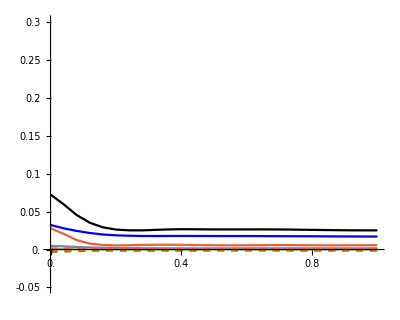

```mathematica
(*Plotting*)
ListPlot[{TotenvTotenv,CouCou,PolPol,ExrExr,DisDis,CouPol,CouExr,CouDis,ExrPol,ExrDis,PolDis},Joined-> True,PlotRange-> {{0,1},{-0.05,0.301}},AspectRatio->0.8,AxesStyle-> Directive[Black,Thickness-> 0.004],Ticks-> {Table[i,{i,0,1,0.2}],Table[i,{i,-0.05,0.30,0.05}]},TicksStyle->Directive[Black,FontSize-> 16,Thickness-> 0.005],AxesOrigin->{0,0},PlotStyle->{{Black},{Blue},{},{},{},{Dashed},{Dashed},{Dashed},{Dashed},{Dashed},{Dashed}}]
```